# Tree-level graviton scattering with FeynArts

Generate and display all four off-shell 2 -> 2 graviton tree diagrams with FeynArts: the three exchange channels and the quartic contact. Attach unconstrained external polarisation tensors, contract each contribution, and store their sum in ℳ. No mass-shell, transversality, tracelessness or helicity conditions are imposed.

## 1. Initialisation

Start with a fresh kernel (especially after running the previous on-shell version) and evaluate the cell below with Shift+Enter. FeynGrav loads FeynCalc and CalcFormConverter; setting $LoadFeynArts first also loads the installed FeynCalc-patched FeynArts. The saved pure-GR model uses gauge parameter 2 and contains the cubic and quartic graviton interactions and gravitational ghosts. No diagrams are generated and FORM is not executed here. Opening this notebook executes nothing.

```mathematica
$LoadFeynArts=True;feynGravDirectory=ExpandFileName[FileNameJoin[{NotebookDirectory[],".."}]];Get[FileNameJoin[{feynGravDirectory,"FeynGrav.wl"}]];FeynGrav`importGravitons[2];grModelDirectory=FileNameJoin[{feynGravDirectory,"Benchmark","FeynArtsEvidence","model-first-2026-10-12","model"}];grModel="FGPureGR5a149c98161e2b2e";FeynArts`$ModelPath=Prepend[DeleteCases[FeynArts`$ModelPath,grModelDirectory],grModelDirectory];If[FeynArts`InitializeModel[grModel,FeynArts`GenericModel->grModel,FeynArts`Reinitialize->False]=!=True,Print["The pure-GR model could not be loaded. Check grModelDirectory and restart with a fresh kernel."];Abort[]];
```

## 2. Generate and display the contributing diagrams

Including both cubic and quartic vertices generates the s-, t- and u-channel exchanges and the four-graviton contact. Do not select a single channel. The diagram sheet is displayed before CreateFeynAmp or any FORM calculation is called.

```mathematica
treeTopologies=FeynArts`CreateTopologies[0,2->2,FeynArts`Adjacencies->{3,4}];treeInsertions=FeynArts`InsertFields[treeTopologies,{FeynArts`T[1],FeynArts`T[1]}->{FeynArts`T[1],FeynArts`T[1]},FeynArts`Model->grModel,FeynArts`GenericModel->grModel,FeynArts`InsertionLevel->{FeynArts`Classes}];
```

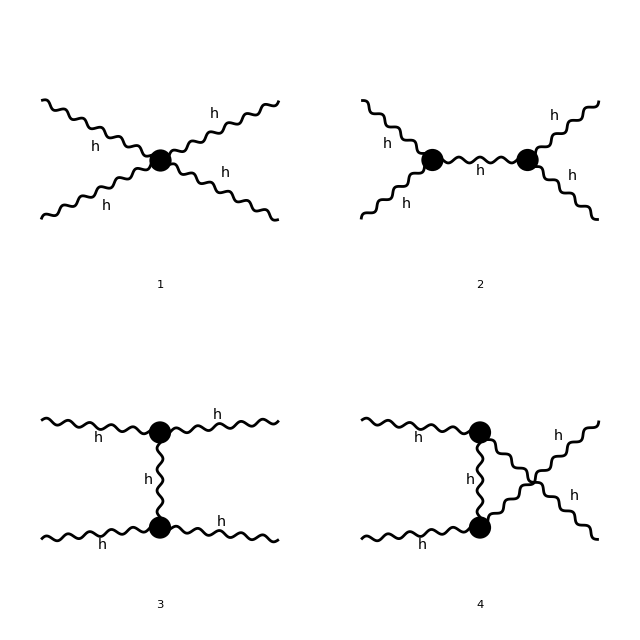

```mathematica
diagramGraphics=FeynArts`Paint[treeInsertions,FeynArts`ColumnsXRows->{2,2},FeynArts`Numbering->FeynArts`Simple,FeynArts`SheetHeader->"Four-graviton tree diagrams",FeynArts`AutoEdit->False,DisplayFunction->Identity];diagramSheet=Show[First[Show[diagramGraphics]],ImageSize->640]
```

Paint supplies the actual inserted FeynArts diagrams. The four numbers identify the contact and three exchange contributions; they are not extra multiplicative weights. FeynArts already supplies the graph factors.

## 3. Build the four off-shell amplitudes

Use incoming momenta p1,p2 and outgoing momenta p3,p4. All virtualities and scalar products remain symbolic. MomentumConservation -> True supplies internal routing at each vertex without imposing mass-shell conditions or eliminating an external momentum. Truncated -> True removes external propagators; polarisations are attached explicitly in the next cell.

```mathematica
treeRawAmplitude=FeynArts`CreateFeynAmp[treeInsertions,FeynArts`PreFactor->1,FeynArts`GaugeRules->{},FeynArts`MomentumConservation->True,FeynArts`Truncated->True];diagramTensors=FCFAConvert[treeRawAmplitude,IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},LorentzIndexNames->{mu1,nu1,mu2,nu2,mu3,nu3,mu4,nu4,alpha1,beta1,alpha2,beta2},ChangeDimension->D,Contract->False,List->True,Prefactor->1];If[!ListQ[diagramTensors]||Length[diagramTensors]=!=4,Print["Expected the contact and three exchange diagrams."];Abort[]];
```

PolarizationTensorD represents the formal factorised tensor epsilon^mu epsilon^nu. Neither p.epsilon nor epsilon.epsilon is set to zero; no normalisation or helicity is chosen. I and -I specify incoming polarisations and conjugated outgoing polarisations, not helicities.

```mathematica
externalTensors=PolarizationTensorD[p1,mu1,nu1,ⅈ,Transversality->False] PolarizationTensorD[p2,mu2,nu2,ⅈ,Transversality->False] PolarizationTensorD[p3,mu3,nu3,-ⅈ,Transversality->False] PolarizationTensorD[p4,mu4,nu4,-ⅈ,Transversality->False];
```

## 4. Contract each diagram and form the total ℳ

Contract the diagrams separately with FORM to limit intermediate expression sizes. The list diagramAmplitudes retains the individual scalar-product expressions. No scalar-product assignments, helicity tables, mass-shell conditions or extra graph factors are introduced. FORM uses one worker and a 60-second per-stage limit; job files are retained under treeWorkDirectory.

```mathematica
Clear[diagramAmplitudes,ℳ];treeWorkDirectory=CreateDirectory[FileNameJoin[{$TemporaryDirectory,"fgfa-four-tree-offshell-"<>CreateUUID[]}]];diagramAmplitudes=Function[tensor,Module[{result},result=CalcFormCalculate[FeynAmpDenominatorExplicit[tensor] externalTensors,Dimension->D,FORMThreads->1,TimeConstraint->60,WorkingDirectory->treeWorkDirectory,KeepFiles->True,ShowProgress->False];If[FailureQ[result]||MemberQ[{$Failed,$Aborted},result]||!FreeQ[result,_LorentzIndex|_CalcFormCalculate],Print["A diagram contraction did not complete. Inspect treeWorkDirectory."];Abort[]];result]]/@diagramTensors;
```

```mathematica
If[!ListQ[diagramAmplitudes]||Length[diagramAmplitudes]=!=4,Print["All four diagram amplitudes must be calculated before summing."];Abort[]];ℳ=Total[diagramAmplitudes];
```

The complete polarisation-contracted, amputated off-shell tree expression is stored in ℳ (Mathematica's ScriptCapitalM symbol). Its preview below is shortened only for display. This is not yet an on-shell physical scattering amplitude: the external virtualities, longitudinal contractions and trace terms remain unconstrained. No loop measure or spin sum is included.

```mathematica
Short[ℳ,4]
```